```mathematica
Select[EdgeList[ReadGrof[1]],#[[1]]==1&]
```

{1<->2,1<->3,1<->4}

```mathematica
Take[deps1,5]
```

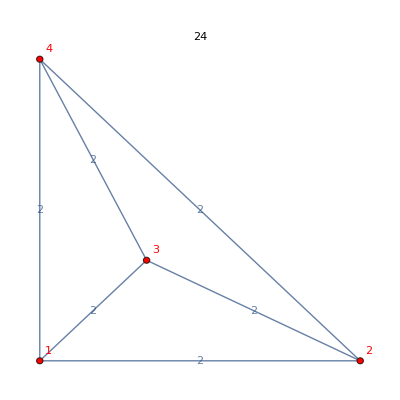
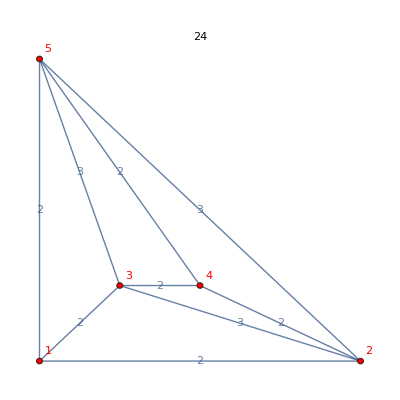
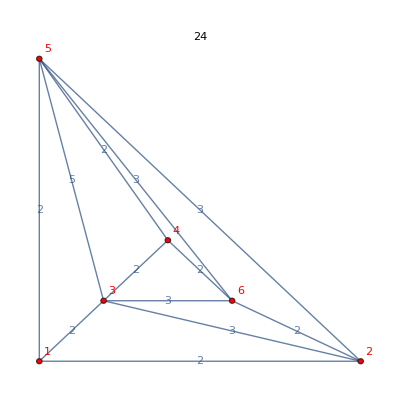
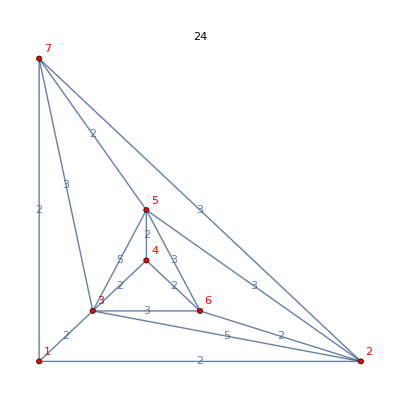
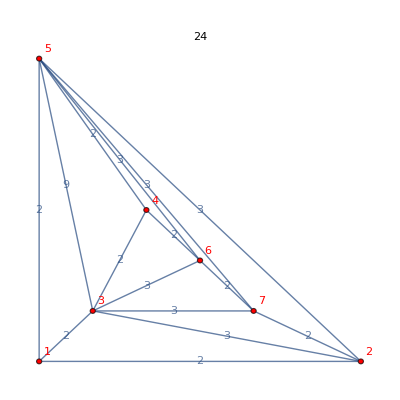
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Map[Row[{
PaintEdgeWeight[ReadGrof[#[[1]]]],PaintEdgeWeight[ReadGrof[#[[2]]]]
}]&, Take[deps1,5]]
```

```mathematica
info=Monitor[
Table[
 With[{
g=ReadGrof[deps2[[k,1]]]},
{VertexCount[g], Chrom[deps2[[k,1]]], Chrom[deps2[[k,2]]],deps2[[k,1]],deps2[[k,2]]}],
{k,1,Length[deps2]}
],
k]
```

{{4,24,24,1,2},{5,24,24,2,3},{5,24,96,2,4},{6,24,24,3,5},{6,24,96,3,6},{6,24,120,3,7},{6,24,24,3,8},{6,96,120,4,7},{7,24,24,5,10},{7,24,120,5,11},{7,24,24,5,12},{7,24,24,5,13},{7,24,96,5,14},{7,24,96,5,15},{7,96,120,6,11},{7,96,72,6,18},{7,96,96,6,14},201449,{13,48,144,19084,95047},{13,48,120,19084,95048},{13,48,120,19084,95049},{13,48,48,19084,95050},{13,48,48,19084,95051},{13,48,48,19084,95052},{13,48,216,19084,94563},{13,48,120,19084,95053},{13,48,216,19084,95054},{13,48,192,19084,89328},{13,48,48,19084,95055},{13,48,192,19084,95056},{13,48,144,19084,95057},{13,48,120,19084,95058},{13,48,192,19084,95059},{13,48,144,19084,95060}}
 |  |  |  |

```mathematica
Length[deps2]
```

201482

```mathematica
Table[
Max[Map[#[[2]]&,Select[info,#[[1]]==k&& #[[2]]<=#[[3]]&]]],
{k,4,13}]/24
```

{1,1,4,5,12,21,44,85,172,48}

```mathematica
{24,24,96,120,288,504,1056}/24
```

{1,1,4,5,12,21,44}

```mathematica
Select[info,#[[1]]==4&& #[[2]]<=#[[3]]&]
```

{{4,24,24,1,1},{4,24,24,1,2}}

```mathematica
MatrixForm[
Table[
Map[{k,#/24}&,Sort[DeleteDuplicates[
Map[#[[2]]&,Select[info,#[[1]]==k&& #[[2]]<=#[[3]]&]]
]]],
{k,4,13}]
]
```

({{4,1}}
{{5,1}}
{{6,1},{6,4}}
{{7,1},{7,4},{7,5}}
{{8,1},{8,3},{8,4},{8,5},{8,12}}
{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,9},{9,12},{9,16},{9,21}}
{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,11},{10,12},{10,13},{10,14},{10,16},{10,20},{10,21},{10,28},{10,44}}
{{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{11,7},{11,8},{11,9},{11,10},{11,11},{11,12},{11,13},{11,14},{11,16},{11,17},{11,20},{11,21},{11,22},{11,25},{11,28},{11,29},{11,40},{11,41},{11,44},{11,48},{11,85}}
{{12,1},{12,2},{12,3},{12,4},{12,5},{12,6},{12,7},{12,8},{12,9},{12,10},{12,11},{12,12},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{12,26},{12,27},{12,28},{12,29},{12,30},{12,32},{12,33},{12,36},{12,37},{12,38},{12,40},{12,41},{12,43},{12,44},{12,45},{12,48},{12,51},{12,54},{12,60},{12,62},{12,64},{12,76},{12,84},{12,85},{12,92},{12,172}}
{{13,1},{13,2},{13,3},{13,4},{13,5},{13,6},{13,7},{13,8},{13,9},{13,10},{13,11},{13,12},{13,13},{13,14},{13,16},{13,17},{13,20},{13,22},{13,25},{13,28},{13,29},{13,40},{13,41},{13,48}})

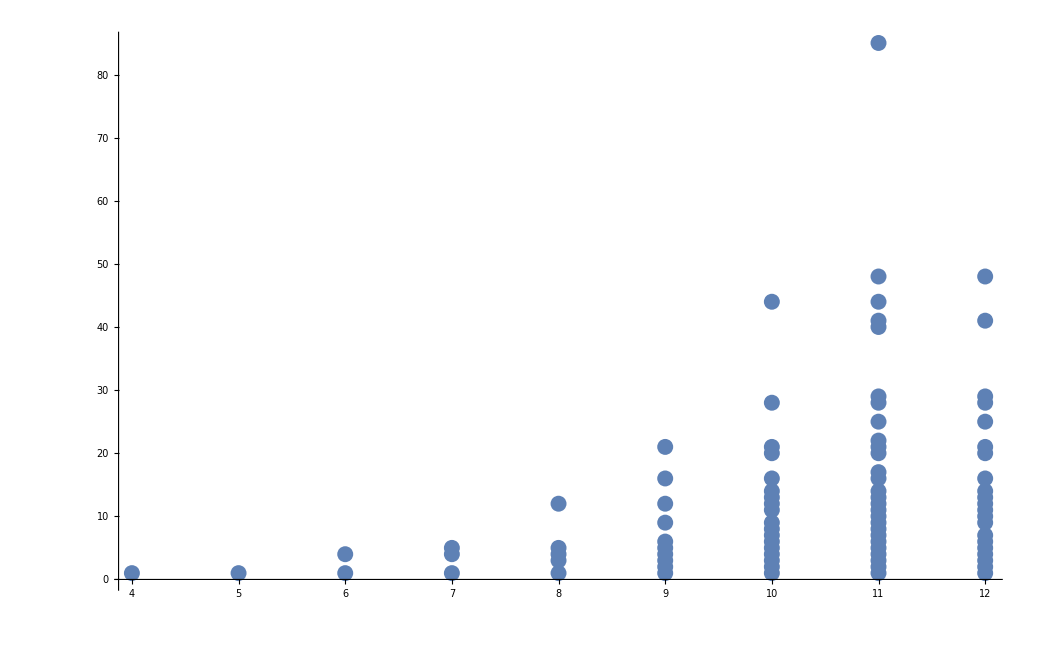

```mathematica
ListPlot[
Flatten[
Table[
Map[{k,#/24}&,Sort[DeleteDuplicates[
Map[#[[2]]&,Select[info,#[[1]]==k&& #[[2]]<=#[[3]]&]]
]]],
{k,4,12}],1], PlotRange->All
]
```